```mathematica
(*Use HoldComplete[FullForm[...]] to see underlying code *)

Subscript[K, 1] = 1;
Subscript[K, 3]= 1.2;
Subscript[K, 2]= 3.0;
Subscript[ϕ, 0]= Pi/4;

g[x_]:=Cos[x]^2(Subscript[K, 2] Cos[x]^2+ Subscript[K, 3] Sin[x]^2)
f[x_]:= Subscript[K, 1] Cos[x]^2+ Subscript[K, 3] Sin[x]^2

g[.5]

G[u_, θ_]:=√(f[u]/(g[u](g[u]-g[θ])))
```

1.99182

```mathematica
W[θ_]:=Chop[Sqrt[g[θ]]NIntegrate[G[u,θ], {u, 0,θ}] ,0.0001] - Subscript[ϕ, 0]
```

```mathematica
W[.7]
```

0.0103002

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.00003208911021472409559443431366726629226117633447712407246399379801}. NIntegrate obtained 0.413868  + 2.77894×10^-6\ ⅈ and 8.69666×10^-6 for the integral and error estimates.

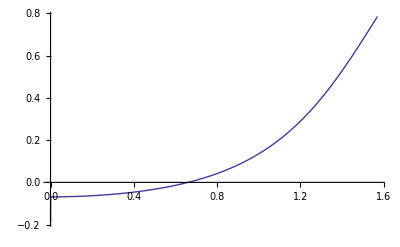

```mathematica
Plot[W[u], {u, 0, Pi/2}]
```

```mathematica
M= th /. FindRoot[W[th], {th,.5, 0, Pi/2}, Evaluated->False]
```

0.660543

```mathematica
W[M]
```

7.22374×10^-9

```mathematica
b = Chop[2Sqrt[g[M]]NIntegrate[Sqrt[(f[u]g[u])/(g[u]-g[M])],{u, 0, M}], 0.0001]
```

3.22589

```mathematica
γ = Sqrt[4 Subscript[K, 2] Subscript[ϕ, 0]^2 g[M]]
```

3.27408

```mathematica
Subscript[G, 1][u_, h_]:=√(g[u]f[u]/(g[u]-g[h]))
```

```mathematica
P[θ_] := NIntegrate[Subscript[G, 1][u, M],{u, 0, θ}]
```

```mathematica
P[0.1]
```

0.139436

```mathematica
R[θ_, y_]:=√g[M]*P[θ]-b*y
```

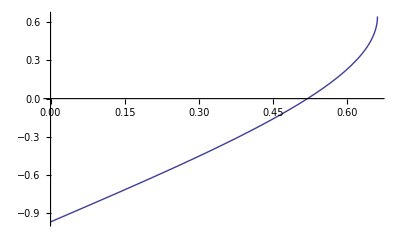

```mathematica
Plot[R[θ, .3], {θ, 0, M}]
```

```mathematica
R[.4,.3]
```

-0.261362

```mathematica
H[y_]:=θ/. FindRoot[R[θ, y],{θ, 0, M}, Evaluated->False]
```

```mathematica
H[.3]
```

0.519161

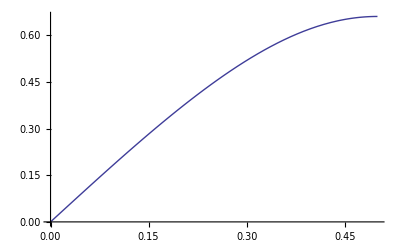

```mathematica
Plot[H[y], {y, 0, .5}]
```

```mathematica
J[y_]:= -Subscript[ϕ, 0]+ Sqrt[g[M]]NIntegrate[G[u,M], {u, 0, H[y]}]
```

```mathematica
J[0.5]
```

7.22374×10^-9

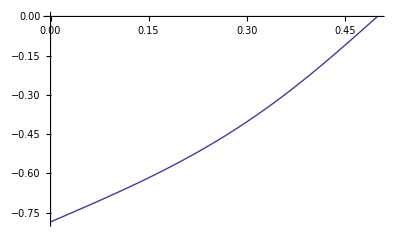

```mathematica
Plot[J[y], {y, 0, .5}]
```

```mathematica
J[.5]
```

7.22374×10^-9

```mathematica
nx[y_] := Cos[H[y]]Cos[J[y]]
ny[y_] :=Sin[H[y]]
nz[y_]:= Cos[H[y]]Sin[J[y]]
```

```mathematica
nx[0.017358]
ny[0.017358]
nz[0.017358]
```

0.719786

0.033449

-0.69339

```mathematica
nx[0.017358]^2+ ny[0.017358]^2+ nz[0.017358]^2
```

1.